```mathematica
DGPSystem[G_Graph,K_Integer]:=Block[{x,y,theSystem},x=Array[y,{Length[VertexList[G]],K}];
theSystem=Map[(Sqrt[Sum[(x[[#[[1]],k]]-x[[#[[2]],k]])^2,{k,K}]]==WeightedAdjacencyMatrix[G][[#[[1]],#[[2]]]])&,EdgeList[G]];
Return[theSystem]]

DGPSystemSquared[G_Graph,K_Integer]:=Block[{x,y,theSystem},x=Array[y,{Length[VertexList[G]],K}];
theSystem=Map[(Sum[(x[[#[[1]],k]]-x[[#[[2]],k]])^2,{k,K}]==(WeightedAdjacencyMatrix[G][[#[[1]],#[[2]]]])^2)&,EdgeList[G]];
Return[theSystem]]

DGPSystemAbs[G_Graph,K_Integer]:=Block[{x,y,theSystem},x=Array[y,{Length[VertexList[G]],K}];
theSystem=Map[(EuclideanDistance[x[[#[[1]]]],x[[#[[2]]]]]==WeightedAdjacencyMatrix[G][[#[[1]],#[[2]]]])&,EdgeList[G]];
Return[theSystem]]

DGPSystemSquaredAbs[G_Graph,K_Integer]:=Block[{x,y,theSystem},x=Array[y,{Length[VertexList[G]],K}];
theSystem=Map[((EuclideanDistance[x[[#[[1]]]],x[[#[[2]]]]])^2==(WeightedAdjacencyMatrix[G][[#[[1]],#[[2]]]])^2)&,EdgeList[G]];
Return[theSystem]]

(*---------*)

DGPSystemVars[G_Graph,K_Integer,y_]:=Block[{theSystem},theSystem=Map[(Sqrt[Sum[(y[[#[[1]],k]]-y[[#[[2]],k]])^2,{k,K}]]==WeightedAdjacencyMatrix[G][[#[[1]],#[[2]]]])&,EdgeList[G]];
Return[theSystem]]

DGPSystemSquaredVars[G_Graph,K_Integer,y_]:=Block[{theSystem},theSystem=Map[(Sum[(y[[#[[1]],k]]-y[[#[[2]],k]])^2,{k,K}]==(WeightedAdjacencyMatrix[G][[#[[1]],#[[2]]]])^2)&,EdgeList[G]];
Return[theSystem]]
```

```mathematica
G=Graph[{1<->2,2<->3,3<->1,1<->4,4<->2},VertexLabels->"Name",EdgeWeight->{1,2,2,1,1}]
K=2
```

-Graphics-

2

```mathematica
myVars=Array[x,{Length[VertexList[G]],K}]
```

{{x[1,1],x[1,2]},{x[2,1],x[2,2]},{x[3,1],x[3,2]},{x[4,1],x[4,2]}}

```mathematica
S=DGPSystemSquaredVars[G,K,myVars]
```

{(x[1,1]-x[2,1])^2+(x[1,2]-x[2,2])^2==1,(x[2,1]-x[3,1])^2+(x[2,2]-x[3,2])^2==4,(-x[1,1]+x[3,1])^2+(-x[1,2]+x[3,2])^2==4,(x[1,1]-x[4,1])^2+(x[1,2]-x[4,2])^2==1,(-x[2,1]+x[4,1])^2+(-x[2,2]+x[4,2])^2==1}

```mathematica
IncongruentSolutions={x[1,1]->0,x[1,2]->0,x[2,1]->1}
SI=S/.IncongruentSolutions
sol=Solve[Apply[And,SI],Flatten[myVars],Reals]
```

{x[1,1]→0,x[1,2]→0,x[2,1]→1}

{1+x[2,2]^2==1,(1-x[3,1])^2+(x[2,2]-x[3,2])^2==4,x[3,1]^2+x[3,2]^2==4,x[4,1]^2+x[4,2]^2==1,(-1+x[4,1])^2+(-x[2,2]+x[4,2])^2==1}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x[2,2]→0,x[3,1]→1/2,x[3,2]→-(√15)/2,x[4,1]→1/2,x[4,2]→-(√3)/2},{x[2,2]→0,x[3,1]→1/2,x[3,2]→-(√15)/2,x[4,1]→1/2,x[4,2]→(√3)/2},{x[2,2]→0,x[3,1]→1/2,x[3,2]→(√15)/2,x[4,1]→1/2,x[4,2]→-(√3)/2},{x[2,2]→0,x[3,1]→1/2,x[3,2]→(√15)/2,x[4,1]→1/2,x[4,2]→(√3)/2}}

```mathematica
sol2 = myVars /. IncongruentSolutions /.sol
```

{{{0,0},{1,0},{1/2,-(√15)/2},{1/2,-(√3)/2}},{{0,0},{1,0},{1/2,-(√15)/2},{1/2,(√3)/2}},{{0,0},{1,0},{1/2,(√15)/2},{1/2,-(√3)/2}},{{0,0},{1,0},{1/2,(√15)/2},{1/2,(√3)/2}}}

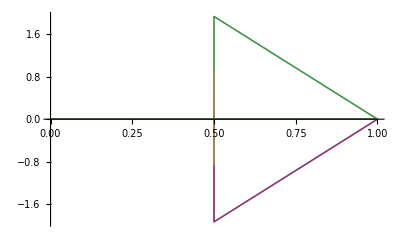

```mathematica
ListPlot[sol2, Joined ->True]
```

-Graphics-

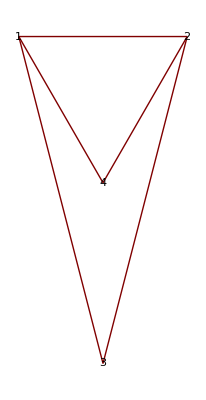
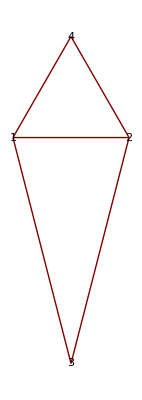
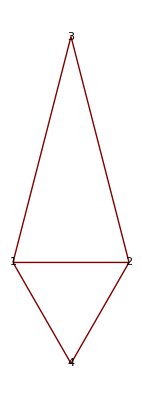
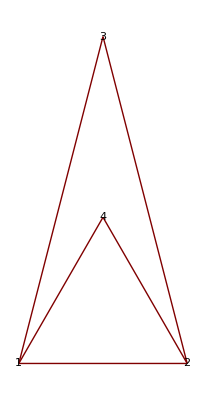

```mathematica
Print[G]
Map[GraphPlot[G, VertexLabeling->True, VertexCoordinateRules->#]&, sol2]
```